## Solving the analytical mixing model...! Last updated: February 20, 2019

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n
f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ2A,η])*(n/2-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ1A,η])*(n/2-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ2B,η])*(n/2-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ1B,η])*(n/2-(n1B+n2B)) - τ*n2B
```

```mathematica
f1p = f1/.n1B->0
f2p = f2/.n2B->0
f3p
f4p
```

-(n1A α1A)/n+δ1

-(n2A α2A)/n+δ2

((n/2-n1A-n2A) s1^η (2-s2^η/(s2^η+μ2A^η)))/(2 (s1^η+μ1A^η))-n1A τ

((n/2-n1A-n2A) s2^η (2-s1^η/(s1^η+μ1A^η)))/(2 (s2^η+μ2A^η))-n2A τ

```mathematica
(*η=7;
MatrixForm[N@{s1/n,s2/n}/.Solve[(f1p/.{δ1->0.6,δ2->0.6,α1A->2,α2A ->2,τ->0.2,μ1A->10,μ2A->10})==0&&(f2p/. {δ1->0.6,δ2->0.6,α1A ->2,α2A ->2,τ->0.2,μ1A->10,μ2A->10})==0&&(f3p/. {δ1->0.6,δ2->0.6,α1A ->2,α2A ->2,τ->0.2,μ1A->10,μ2A->10})==0&&(f4p/. {δ1->0.6,δ2->0.6,α1A ->2,α2A ->2,τ->0.2,μ1A->10,μ2A->10})==0,{s1,s2,n1A,n2A}]/.n->16]
*)
```

```mathematica
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}≥0;
```

```mathematica
soln12A= Solve[f1p == 0 && f2p == 0,{n1A,n2A}]
```

{{n1A→(n δ1)/α1A,n2A→(n δ2)/α2A}}

```mathematica
f3pp =f3p /.soln12A[[1]]
f4pp =f4p /.soln12A[[1]]
Solve[f3pp==0 && f4pp==0,{s1,s2}];
```

(s1^η (n/2-(n δ1)/α1A-(n δ2)/α2A) (2-s2^η/(s2^η+μ2A^η)))/(2 (s1^η+μ1A^η))-(n δ1 τ)/α1A

(s2^η (n/2-(n δ1)/α1A-(n δ2)/α2A) (2-s1^η/(s1^η+μ1A^η)))/(2 (s2^η+μ2A^η))-(n δ2 τ)/α2A

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

So we can get a solution, but we don’t know what the solution looks like.

```mathematica
Clear[η]
δ1:=δ
δ2:=δ

(* Sanity check *)
((f3pp + f4pp)-((s1^η/(s1^η+μ1A^η)+s2^η/(s2^η+μ2A^η)-s1^η/(s1^η+μ1A^η)*s2^η/(s2^η+μ2A^η))(n/2-n δ(1/α1A+1/α2A)) -n δ τ(1/α1A+1/α2A)) )// FullSimplify
((f3pp - f4pp) -((s1^η/(s1^η+μ1A^η)-s2^η/(s2^η+μ2A^η))(n/2-n δ(1/α1A+1/α2A)) -n δ τ(1/α1A-1/α2A)))// FullSimplify
```

0

0

Great, so we can define the new LHS’s as follows:

```mathematica
K1:=s1^η/(s1^η+μ1A^η)
K2:=s2^η/(s2^η+μ2A^η)
```

```mathematica
sumf := (K1+K2-K1*K2)(n/2-n δ(1/α1A+1/α2A)) -n δ τ(1/α1A+1/α2A)
diff := (K1-K2)(n/2-n δ(1/α1A+1/α2A)) -n δ τ(1/α1A-1/α2A)
```

```mathematica
Clear[K1,K2]
K1sol2 = Solve[diff==0,K1][[1]];
Reduce[(K1/.K1sol )== K2 + (2δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A))]
```

ReplaceAll::reps: {K1sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

α1A α2A-2 α1A δ-2 α2A δ≠0&&K2==(2 α1A δ τ-2 α2A δ τ+α1A α2A (K1/.K1sol)-2 α1A δ (K1/.K1sol)-2 α2A δ (K1/.K1sol))/(α1A α2A-2 α1A δ-2 α2A δ)

Great, so we can substitute the following for K1:

```mathematica
K1 = K2 + (2δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A));
```

Now we want to check if the expression for K2 derived analytically is correct. (K2ap = analytical, positive; K2an = analytical, negative)

```mathematica
K2ap =( 1- (δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A))) + √(( 1- (δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A)))^2-(4δ τ(1/α2A))/(1- 2δ(1/α1A+1/α2A)))
K2an =( 1- (δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A))) - √(( 1- (δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A)))^2-(4δ τ(1/α2A))/(1- 2δ(1/α1A+1/α2A)));
```

1-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ)+√(-(4 δ τ)/(α2A (1-2 (1/α1A+1/α2A) δ))+(1-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ))^2)

Let’s check by substitution:

```mathematica
sumf/.K2->K2ap // FullSimplify
sumf/.K2->K2an // FullSimplify
```

0

0

So far so good; the analytically computed values of K2 both satisfy the condition sumf == 0. What about the K1’s?

```mathematica
K1ap =( 1+ (δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A))) + √(( 1- (δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A)))^2-(4δ τ(1/α2A))/(1- 2δ(1/α1A+1/α2A)));
K1an =( 1+ (δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A))) - √(( 1- (δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A)))^2-(4δ τ(1/α2A))/(1- 2δ(1/α1A+1/α2A)));
```

This one is easier, given the relation K1 = K2 + (2δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A)):

```mathematica
(K1/.K1->K1ap)-(K2/.K2->K2ap + (2δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A))) // FullSimplify
(K1/.K1->K1an)-(K2/.K2->K2an + (2δ τ(1/α1A-1/α2A))/(1- 2δ(1/α1A+1/α2A))) // FullSimplify
```

0

0

Worth noting that K1ap corresponds to K2ap and K1an to K2an.
Note that we haven’t made any assumptions about μ’s or α’s.  The only assumption we have made so far is that the δ’s are equal (which we could probably relax eventually but it’s not crucial from the modeling standpoint).
So we now just need to solve for the actual values of s1 and s2, right? We bring back the original relations, K1=s1^η/(s1^η+μ1A^η)and K2=s2^η/(s2^η+μ2A^η)

Looks like this is where Mathematica is not very smart.

```mathematica
Clear[η] (*Checking*)
```

```mathematica
s1comp = Solve[K1dummy==s1^η/(s1^η+μ1A^η),s1][[1]] // FullSimplify
s2comp = Solve[K2dummy==s2^η/(s2^η+μ2A^η),s2][[1]] // FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{s1→(-((-1+K1dummy) μ1A^-η)/K1dummy)^(-1/η)}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{s2→(-((-1+K2dummy) μ2A^-η)/K2dummy)^(-1/η)}

```mathematica
(μ1A(-1+1/(1-K1dummy))^(1/η) -(s1/.s1sol) )/.η->1// FullSimplify
```

ReplaceAll::reps: {s1sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(K1dummy μ1A)/(1-K1dummy)-(s1/.s1sol)

For example, Mathematica can' t see in general that two terms in the parentheses above are identical.  But it works okay when we set η  = integer, so we will do that for now.

```mathematica
s1sol := μ1A(-1+1/(1-K1dummy))^(1/η)
s2sol := μ2A(-1+1/(1-K2dummy))^(1/η)
```

```mathematica
η=1;
```

```mathematica
s1subp=(s1/.s1-> s1sol)/.K1dummy->K1ap
s2subp=(s2/.s2-> s2sol)/.K2dummy->K2ap

s1subn=(s1/.s1-> s1sol)/.K1dummy->K1an
s2subn=(s2/.s2-> s2sol)/.K2dummy->K2an
```

μ1A (-1+1/(-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ)-√(-(4 δ τ)/(α2A (1-2 (1/α1A+1/α2A) δ))+(1-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ))^2)))

μ2A (-1+1/(((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ)-√(-(4 δ τ)/(α2A (1-2 (1/α1A+1/α2A) δ))+(1-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ))^2)))

μ1A (-1+1/(-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ)+√(-(4 δ τ)/(α2A (1-2 (1/α1A+1/α2A) δ))+(1-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ))^2)))

μ2A (-1+1/(((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ)+√(-(4 δ τ)/(α2A (1-2 (1/α1A+1/α2A) δ))+(1-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ))^2)))

So these are the exact solutions to the system, yay.
We need these stimuli to be real numbers. What is the condition for that?  We need, at the very least, the expressions under the square roots to be positive.  Ok.

But before we check these, let’s do a sanity check, at least in the η = 1 case.

```mathematica
Solve[f3pp==0 && f4pp==0,{s1,s2}] /. {δ->0.6,α1A ->1.44,α2A ->1.44,τ->0.2,μ1A->10,μ2A->10}// Chop
{{s1subn,s2subn},{s1subp,s2subp}}/. {δ->0.6,α1A ->1.44,α2A ->1.44,τ->0.2,μ1A->10,μ2A->10} // Chop
```

{{s1→-18.165,s2→-18.165},{s1→-1.83503,s2→-1.83503}}

{{-1.83503,-1.83503},{-18.165,-18.165}}

So far so good.

What we are looking for is the condition under which 0≤-(4 δ τ)/(α2A (1-2 (1/α1A+1/α2A) δ))+(1-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ))^2 is satisfied.  
Where are the two sides equal?

```mathematica
1/(1-2 (k1+k2) δ)(-4 δ τ k2+(1-2 (k1+k2) δ-(k1-k2) δ τ)^2/(1-2 (k1+k2) δ))
```

(-4 k2 δ τ+(1-2 (k1+k2) δ-(k1-k2) δ τ)^2/(1-2 (k1+k2) δ))/(1-2 (k1+k2) δ)

```mathematica
Solve[1/(1-2 (K) δ)(-4 δ τ k2+(1-2 (K) δ-(k1-k2) δ τ)^2/(1-2 (K) δ))==0,K]
```

{{K→(1-k1 δ τ-2 √k1 √k2 δ τ-k2 δ τ)/(2 δ)},{K→(1-k1 δ τ+2 √k1 √k2 δ τ-k2 δ τ)/(2 δ)}}

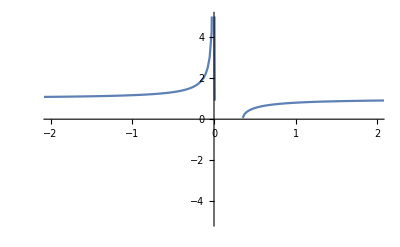

```mathematica
Plot[(√(-z/x+(1-y/x)^2))/.{y->0.06,z->0.24},{x,-10,10},PlotRange->{{-2,2},{-5,5}},MaxRecursion->4]
```

```mathematica
x :=(1-2 (1/α1A+1/α2A)δ)/(δ τ)
y:=(1/α1A-1/α2A) 
z := 4(1/α2A)
F :=(√(-z/x+(1-y/x)^2))

(*Check this expression*)
F-(√(-(4 δ τ(1/α2A))/(1-2 (1/α1A+1/α2A) δ)+(1-((1/α1A-1/α2A) δ τ)/(1-2 (1/α1A+1/α2A) δ))^2))
```

0

```mathematica
Clear[x,y,z]
F//FullSimplify
solxyz=Solve[(x-y)^2-x z==0,y]
```

√(((x-y)^2-x z)/x^2)

{{y→x-√x √z},{y→x+√x √z}}

```mathematica
x :=(1-2 (1/α1A+1/α2A)δ)/(δ τ)
y:=(1/α1A-1/α2A) 
z := 4(1/α2A)
(x-y)^2-x z
solxyz/. {δ->0.6,α1A ->1.44,α2A ->1.44,τ->0.2,μ1A->10,μ2A->10} // FullSimplify
```

(-1/α1A+1/α2A+(1-2 (1/α1A+1/α2A) δ)/(δ τ))^2-(4 (1-2 (1/α1A+1/α2A) δ))/(α2A δ τ)

{{0.→-5.55556-3.92837 ⅈ},{0.→-5.55556+3.92837 ⅈ}}